```mathematica
d=0.01;m=2500;l=6;K=1000; μ=1.3;λ=0.06;g=9.8;
theta=NDSolve[{θ''[t]==-d θ'[t]-(6K/m)θ[t]+f[t],θ[0]==0.01,θ'[0]==0.2},θ,{t,0,100}]
height=NDSolve[{y''[t]==-d y'[t]-(2K/m)y[t]+g,y'[0]==0.01,y[0]==0.01},y,{t,0,100}]
```

NDSolve[{θ''[t]==f[t]-(12 θ[t])/5-0.01 θ'[t],θ[0]==0.01,θ'[0]==0.2},θ,{t,0,100}]

NDSolve[{0==9.8-(4 5[t])/5,False,5[0]==0.01},5,{t,0,100}]

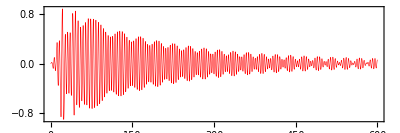

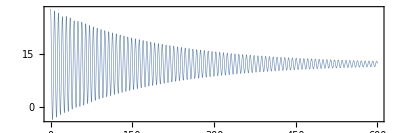

```mathematica
ClearAll["Global‘*"];
d=0.01;m=2500;l=6;K=1000; μ=1.3;λ=0.03;g=9.8;
res=NDSolve[{θ''[t]==-d θ'[t]+3 K/(m l)Cos[θ[t]](Max[y[t]-l Sin[θ[t]],0]    -  Max[y[t]+l Sin[θ[t]],0] )+λ Sin[μ t],
y''[t]==- d y'[t]-(K/m) (Max[y[t]-l Sin[θ[t]],0]    +  Max[y[t]+l Sin[θ[t]],0] )+g,y[0]==28,y'[0]==0,θ[0]==0.001,θ'[0]==0},{θ[t],y[t]},{t,0,1000}];
Plot[θ[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Red,Thickness[0.001]],Frame->True,FrameStyle->Directive[20]]
Plot[y[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Thickness[0.001]],Frame->True,FrameStyle->Directive[20]]
```

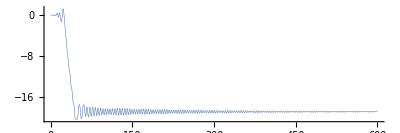

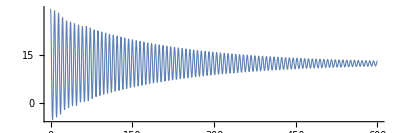

```mathematica
ClearAll["Global‘*"];
d=0.01;m=2500;l=6;K=1000; μ=1.3;λ=0.03;g=9.8;a=0.001;

res=NDSolve[{θ''[t]==-d θ'[t]+3(K/(m l))Cos[θ[t]]((y[t]-l Sin[θ[t]])(1+Tanh[(y[t]-l Sin[θ[t]])/a])/2   - (y[t]+l Sin[θ[t]])(1+Tanh[(y[t]+l Sin[θ[t]])/a])/2  )+λ Sin[μ t],
y''[t]==- d y'[t]-(K/m) ((y[t]-l Sin[θ[t]])(1+Tanh[(y[t]-l Sin[θ[t]])/a])/2    + (y[t]+l Sin[θ[t]])(1+Tanh[(y[t]+l Sin[θ[t]])/a])/2  ) +g,y[0]==29,y'[0]==0,θ[0]==0.001,θ'[0]==0},{θ[t],y[t]},{t,0,1000}];
Plot[θ[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Thickness[0.001]]]
Plot[y[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Thickness[0.002]]]
```

```mathematica
h=0.1;
pics=Table[Graphics[Rotate[Rectangle[{-2,-0.1},{2,0.1}],First[(θ[t]/.res)]],PlotRange->{{-5,5},{-5,5}},ImageSize->Large],{t,20,40,0.033}];
```

```mathematica
Export["simulationmckenna.mov",pics,"FrameRate"->30,ImageSize->Large]
```

simulationmckenna.mov

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["simulationmckenna.mov"]]]
```

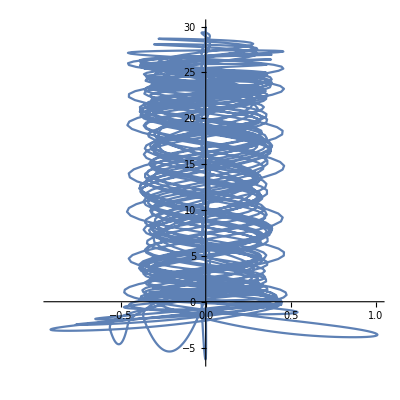

```mathematica
ParametricPlot[{First[θ[t]/.res],First[y[t]/.res]},{t,0,10},AspectRatio->1]
```

```mathematica
m=1000;c=0.01; k=1000; U=18;f=1;k0=2;c0=0.0001;
DSolve[{m x''[t]+(c-c0 U) x'[t]+(k-k0 U) x[t]== f U,x[0]==0,x'[0]==0},x[t],t ]
```

{{x[t]→0.0186722 ⅇ^(-4.1×10^-6 t) (1. ⅇ^(4.1×10^-6 t)-1. Cos[0.981835 t]-4.17585×10^-6 Sin[0.981835 t])}}

```mathematica
Solve[D[0.01867219917012448+ⅇ^(1/2 (-9.999999999999999*^-6+0.018 c0-√(-3.8559999999-3.5999999999786203*^-7 c0+0.00032399999999999996 c0^2)) t),t]==0,t]
```

{}

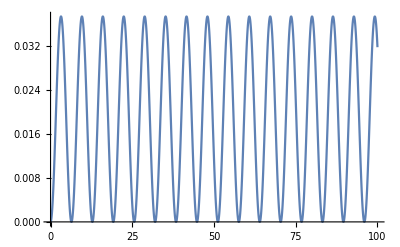

```mathematica
Plot[0.01867219917012448 ⅇ^(-4.1*^-6 t) (1. ⅇ^(4.1*^-6 t)-1. Cos[0.9818350166821257 t]-4.1758543241358*^-6 Sin[0.9818350166821257 t]),{t,0,100}]
```

### Correct vs linear - long term

```mathematica
ClearAll["Global‘*"];
μ=1.2;  λ=0.06;
thetacorr=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==1.3,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
thetaerr=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*θ[t]+λ Sin[μ t],θ[0]==1.3,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
Plot[{θ[t]/.thetacorr},{t,(1000-16)*(2π)/1.2,1000*(2π)/1.2},AspectRatio->1/3,ImageSize->Full,Frame->True,FrameStyle->Directive[20]];
Plot[θ[t]/.thetaerr,{t,(1000-16)*(2π)/1.2,1000*(2π)/1.2},AspectRatio->1/3,ImageSize->Full,PlotRange->{Automatic,{-1,1}},PlotStyle->Red,Frame->True,FrameStyle->Directive[20]];
```

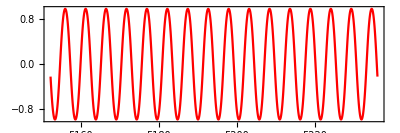

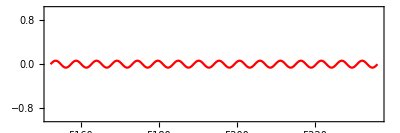

```mathematica
ClearAll["Global‘*"];
μ=1.2;  λ=0.06;
thetalarge=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==1.3,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
thetasmall=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*θ[t]+λ Sin[μ t],θ[0]==1.3,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
Plot[{θ[t]/.thetacorr},{t,(1000-16)*(2π)/1.2,1000*(2π)/1.2},AspectRatio->1/3,ImageSize->Full,Frame->True,FrameStyle->Directive[20],PlotStyle->Red]
Plot[θ[t]/.thetasmall,{t,(1000-16)*(2π)/1.2,1000*(2π)/1.2},AspectRatio->1/3,ImageSize->Full,PlotRange->{Automatic,{-1,1}},PlotStyle->Red,Frame->True,FrameStyle->Directive[20]]
```

```mathematica
ClearAll["Global‘*"];
μ=2.6;  λ=0.073;
thetalarge=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==1.3,θ'[0]==0},θ[t],{t,0,1000*(2π)/μ}];
thetasmall=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==0.8,θ'[0]==0},θ[t],{t,0,1000*(2π)/μ}];
Plot[{θ[t]/.thetalarge,θ[t]/.thetasmall},{t,(1000-16)*(2π)/μ,1000*(2π)/μ},AspectRatio->1/2,ImageSize->Full,PlotRange->{Automatic,{-1.4,1.4}},Frame->True,FrameStyle->Directive[20],PlotStyle->{Red,Blue}];
Plot[θ[t]/.thetasmall,{t,(1000-16)*(2π)/μ,1000*(2π)/μ},AspectRatio->1/2,ImageSize->Full,PlotRange->{Automatic,{-1,1}},PlotStyle->Red,Frame->True,FrameStyle->Directive[20]];
```

```mathematica
ClearAll["Global‘*"];
μ=4;  λ=0.4;
thetalarge=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==1.3,θ'[0]==0},θ[t],{t,0,1000*(2π)/μ}];
thetasmall=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==0.8,θ'[0]==0},θ[t],{t,0,1000*(2π)/μ}];
Plot[{θ[t]/.thetalarge,θ[t]/.thetasmall},{t,(1000-16)*(2π)/μ,1000*(2π)/μ},AspectRatio->1/2,ImageSize->Full,PlotRange->{Automatic,{-1.4,1.4}},Frame->True,FrameStyle->Directive[20],PlotStyle->{Red,Blue}];
Plot[θ[t]/.thetasmall,{t,(1000-16)*(2π)/μ,1000*(2π)/μ},AspectRatio->1/2,ImageSize->Full,PlotRange->{Automatic,{-1,1}},PlotStyle->Red,Frame->True,FrameStyle->Directive[20]];
```

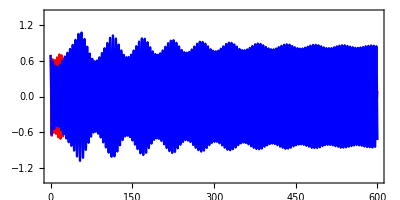

-Graphics-

```mathematica
ClearAll["Global‘*"];
μ=1.3;  λ=0.05;
thetaerr=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4θ[t]+λ Sin[μ t],θ[0]==0.7,θ'[0]==0},θ[t],{t,0,1000*(2π)/μ}];
thetacorr=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==0.7,θ'[0]==0},θ[t],{t,0,1000*(2π)/μ}];
Plot[{θ[t]/.thetaerr,θ[t]/.thetacorr},{t,0,600},AspectRatio->1/2,ImageSize->Full,PlotRange->{{0,600},{-1.4,1.4}},Frame->True,FrameStyle->Directive[20],PlotStyle->{Red,Blue}]
Plot[{θ[t]/.thetasmall},{t,0,600},AspectRatio->1/2,ImageSize->Full,PlotRange->{{0,600},{-1.4,1.4}},Frame->True,FrameStyle->Directive[20],PlotStyle->{Red,Blue}]
```

```mathematica
1(−2+2+λ)-1(−2+2λ+2)+(1−λ)((1−λ)(−2−λ)+2)//FullSimplify
```

-λ^3

```mathematica
CharacteristicPolynomial[{{1,-2,1},{1,-2,1},{1,-2,1}},x]
```

-x^3

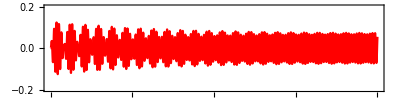

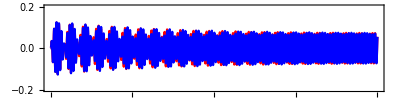

```mathematica
ClearAll["Global‘*"];
μ=1.3;  λ=0.05;
thetacorr=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==0,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
thetaerr=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*θ[t]+λ Sin[μ t],θ[0]==0,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
Plot[{θ[t]/.thetaerr},{t,0,600},AspectRatio->1/4,ImageSize->Full,Frame->True,PlotRange->{Automatic,{-0.2,0.2}},FrameStyle->Directive[20],PlotStyle->Red]
Plot[{θ[t]/.thetaerr,θ[t]/.thetacorr},{t,0,600},AspectRatio->1/4,ImageSize->Full,PlotRange->{Automatic,{-0.2,0.2}},PlotStyle->{Red,Blue},Frame->True,FrameStyle->Directive[20]]
```

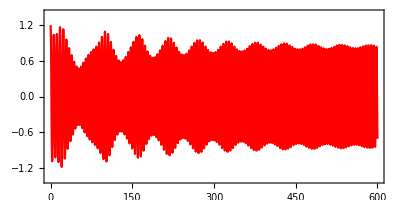

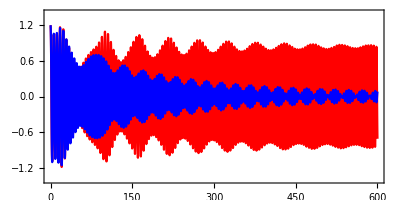

```mathematica
ClearAll["Global‘*"];
μ=1.3;  λ=0.05;
lambdalarge=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==1.2,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
  λ=0.04;
lambdasmall=NDSolve[{θ''[t]==-0.01 θ'[t]-2.4*Cos[θ[t]]Sin[θ[t]]+λ Sin[μ t],θ[0]==1.2,θ'[0]==0},θ[t],{t,0,1000*(2π)/1.2}];
Plot[{θ[t]/.lambdalarge},{t,0,600},AspectRatio->1/2,ImageSize->Full,Frame->True,PlotRange->{{0,600},{-1.4,1.4}},FrameStyle->Directive[20],PlotStyle->Red]
Plot[{θ[t]/.lambdalarge,θ[t]/.lambdasmall},{t,0,600},AspectRatio->1/2,ImageSize->Full,PlotRange->{{0,600},{-1.4,1.4}},PlotStyle->{Red,Blue},Frame->True,FrameStyle->Directive[20]]
```

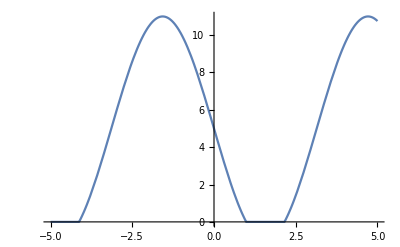

```mathematica
y=5;l=6;a=0.001;
Plot[(y-l Sin[θ])(1+Tanh[(y-l Sin[θ])/a])/2,{θ,-5,5}]
```

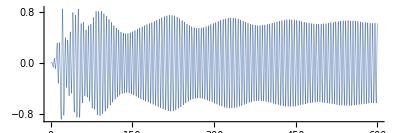

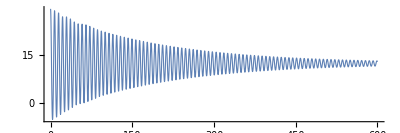

```mathematica
ClearAll["Global‘*"];
d=0.01;m=2500;l=6;K=1000; μ=1.4;λ=0.02;g=9.8;
res=NDSolve[{θ''[t]==-d θ'[t]+3(K/(m l))Cos[θ[t]](Max[y[t]-l Sin[θ[t]],0]    -  Max[y[t]+l Sin[θ[t]],0] )+λ Sin[μ t],
y''[t]==- d y'[t]-(K/m) (Max[y[t]-l Sin[θ[t]],0]    +  Max[y[t]+l Sin[θ[t]],0] )+g,y[0]==29,y'[0]==0,θ[0]==0.001,θ'[0]==0},{θ[t],y[t]},{t,0,1000}];
Plot[θ[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Thickness[0.001]]]
Plot[y[t]/.res,{t,0,600},PlotRange->All,AspectRatio->1/3,ImageSize->Full,PlotStyle->Directive[Thickness[0.002]]]
```

```mathematica
pics=Table[Show[ParametricPlot[{First[θ[t]/.res],First[y[t]/.res]},{t,0,tmax},AspectRatio->1,PlotRange->{{-1,1},{-5,30}},ImageSize->Large,AxesLabel->{"Theta","Height"},AxesStyle->Directive[20],TicksStyle->Directive["Label", 20]],Graphics[{PointSize[Large],Red,Point[{First[(θ[t]/.res)],First[(y[t]/.res)]}/.t->tmax]}]],{tmax,0.001,30,0.0333}];
```

```mathematica
Export["test3.mov",pics,"FrameRate"->60,ImageSize->Large,"VideoEncoding"->"H.264"]
```

test3.mov

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test3.mov"]]]
```

```mathematica
1/30
```

1/30

```mathematica
N[1/30]
```

0.0333333